```mathematica
Needs["MaTeX`"]
SetDirectory[NotebookDirectory[]];
colors={ColorData["BlueGreenYellow"][0.1],ColorData["BlueGreenYellow"][0.4],ColorData["BlueGreenYellow"][0.8]};

SteadyState[R_]:=Module[{ps},
	ps = Table[(-1)^i Det[Drop[R,{2},{i}]],{i,Length@R}];
	ps /= Total[ps];
	ps
]

λcoeffs[R_,input_,e_] := Module[{pss,d,Rsp1,Rstall,pssstall,det,inv,c,λe0,λe1},
pss = SteadyState[R];
d = Length@R;
Rsp1 = R;(Rsp1[[input[[1]],#]]=1) &/@ Range[d];
det = Det[Rsp1];
inv = Inverse[Rsp1];
c = det-R[[input[[2]],input[[1]]]]det inv[[input[[1]],input[[2]]]]+R[[input[[1]],input[[2]]]]det inv[[input[[2]],input[[2]]]]//Expand//Chop;
λe1=(-R[[e[[2]],e[[1]]]](-1)^(e[[1]]+input[[2]])Det[Drop[Rsp1,{input[[2]]},{e[[1]]}]]+R[[e[[1]],e[[2]]]](-1)^(e[[2]]+input[[2]])Det[Drop[Rsp1,{input[[2]]},{e[[2]]}]])/c;
Rstall = R-DiagonalMatrix[Diagonal[R]];Rstall[[input[[2]],input[[1]]]] = 0;Rstall[[input[[1]],input[[2]]]] = 0;
Rstall -= DiagonalMatrix[Total[Rstall]];
pssstall = SteadyState[Rstall];
λe0 = Rstall[[e[[2]],e[[1]]]]pssstall[[e[[1]]]]-Rstall[[e[[1]],e[[2]]]]pssstall[[e[[2]]]];
{λe0,λe1}
]
```

## Figure 1 - panels

```mathematica
R={{0,r12,0,3.9,0,0},{r21,0,3.7,2.1,0,0},{0,4.2,0,2.7,0,3.1},{4.3,1.5,0.2,0,3.1,2.5},{0,0,0,0.4,0,4.5},{0,0,1.2,3.4,0.1,0}};
R-=DiagonalMatrix[Total[R]];
pss=SteadyState[R];
input={1,2};e={3,4};ep={6,5};
{λe0,λe1}=λcoeffs[R,input,e];
{λep0,λep1}=λcoeffs[R,input,ep];
ji=(R[[#2,#1]]pss[[#1]]-R[[#1,#2]]pss[[#2]]&@@@{input})[[1]];
je=(R[[#2,#1]]pss[[#1]]-R[[#1,#2]]pss[[#2]]&@@@{e})[[1]];
jep=(R[[#2,#1]]pss[[#1]]-R[[#1,#2]]pss[[#2]]&@@@{ep})[[1]];
jije=SortBy[Flatten[Table[{ji,je},{r12,0,3,.8},{r21,.1,3,.8}],1],First];
jijep=SortBy[Flatten[Table[{ji,jep},{r12,0,3,.8},{r21,.1,3,.8}],1],First];
```

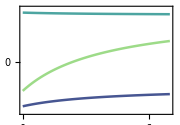

```mathematica
leg=Column[{
LineLegend[{colors[[1]]},{MaTeX["\\jmath_e",FontSize->14]}],
LineLegend[{colors[[2]]},{MaTeX["\\jmath_{e'}",FontSize->14]}]
},Spacings->-0.2];
plot1=Plot[Evaluate[{je,jep,ji}/.r12->1],{r21,0,7},PlotStyle->({#,Opacity[0.8],Thickness[0.01]}&/@colors[[;;3]]),
ImageSize->180,AspectRatio->.7,Axes->False,Frame->True,FrameStyle->Black,LabelStyle->{FontFamily->"Times"},FrameLabel->{{None,None},{MaTeX["r_{+i}",FontSize->14],None}},PlotRange->{{0,7},{-.35,.38}},Epilog->{Inset[MaTeX["\\jmath_{e'}",FontSize->14],Scaled[{.75,.85}]],Inset[MaTeX["\\jmath_{e}",FontSize->14],Scaled[{.75,.1}]],Inset[MaTeX["\\jmath_{i}",FontSize->14],Scaled[{.75,.56}]]},FrameTicks->{{Charting`ScaledTicks["Linear","Nice"][-.5,.5],Automatic},{Charting`ScaledTicks["Linear","Nice"][0,10],Automatic}}]
```

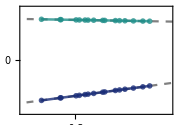

```mathematica
plot2=Show[Plot[λe0+λe1 x,{x,-5,5},PlotStyle->{Gray,Dashed}],
Plot[λep0+λep1 x,{x,-5,5},PlotStyle->{Gray,Dashed}],
ListPlot[{jije,jijep},Joined->True,PlotMarkers->{{Graphics[{colors[[1]],Disk[{0,0}]}],0.05},{Graphics[{colors[[2]],Disk[{0,0}]}],0.05}},PlotStyle->{{colors[[1]],Opacity[0.8],Thickness[0.01]},{colors[[2]],Opacity[0.8],Thickness[0.01]}}],
ImageSize->180,AspectRatio->.7,Axes->False,Frame->True,FrameStyle->Black,LabelStyle->{FontFamily->"Times"},FrameLabel->{{None,None},{MaTeX["\\jmath_i",FontSize->14],None}},PlotRange->{{-.45,.25},{-.45,.45}},Epilog->{Inset[MaTeX["\\jmath_{e'}",FontSize->14],Scaled[{.75,.73}]],Inset[MaTeX["\\jmath_{e}",FontSize->14],Scaled[{.75,.15}]]},FrameTicks->{{Charting`ScaledTicks["Linear","Nice"][-.5,1],Automatic},{Charting`ScaledTicks["Linear","Nice"][-1,.25],Automatic}}]
```

```mathematica
Export["jvsr.png",plot1,"PNG",ImageResolution->700];
Export["jvsj.png",plot2,"PNG",ImageResolution->700];
```